# Chapter 4: The spin-photon interface

## Author: Bruno Ortega Goes

## ??. Pre-measurement analysis: analytics qBhat

```mathematica
ℬqqs = Abs[1-(2 n γ)/(γ+Γ)];
```

### Coherent pulse: all energy range

```mathematica
p0=√(Abs[f0[g,g,t]]^2)/.s->t/.δ->0/.Ω->αdec
```

√(ⅇ^(-1/2 Re[t γ])) Abs[Cos[1/2 t √(-γ^2/4+ⅇ^(-s Γ) n Γ)]+(γ Sin[1/2 t √(-γ^2/4+ⅇ^(-s Γ) n Γ)])/(√(-γ^2+4 ⅇ^(-s Γ) n Γ))]

```mathematica
Limit[p0,s->6γ]
```

ⅇ^(-(t γ)/2) Abs[Cos[1/4 t √(-γ^2+4 ⅇ^(-6 γ Γ) n Γ)]+(γ Sin[1/4 t √(-γ^2+4 ⅇ^(-6 γ Γ) n Γ)])/(√(-γ^2+4 ⅇ^(-6 γ Γ) n Γ))]^2

```mathematica
p0/.t->100γ/.γ->1/.n->nn/.Γ->ΓΓ
```

Abs[Cos[50 √(-1/4+ⅇ^(-s ΓΓ) nn ΓΓ)]+Sin[50 √(-1/4+ⅇ^(-s ΓΓ) nn ΓΓ)]/(√(-1+4 ⅇ^(-s ΓΓ) nn ΓΓ))]/ⅇ^25

```mathematica
classicalqBhatLongRangePlot=ContourPlot[
p0/.t->s/.s->7γ/.γ->1/.n->nn/.Γ->ΓΓ,{nn,0.,10^2},{Γ,10^-2,10^2},
ColorFunction->ColorData[{"TemperatureMap","Reverse"}],
PlotPoints->300,
ScalingFunctions->{"Log","Log"},
FrameTicksStyle->Directive["Times",FontSize->20,Black],
FrameLabel->{Style["Average photon number, n",20,Black],Style["Pulse bandwidth, Γ/γ",20,Black]},
PlotLegends->BarLegend[Automatic,LegendLabel->"ℬ_q",LabelStyle->{"Times",Black,FontSize->20}],
Epilog->Inset[alphabetlabel[[1]],{0.2,5}]]
```

### Restricted bugdet range

```mathematica
classicalqBhatPlot=ContourPlot[
p0test /.t->s/.s->80γ/.γ->1/.n->nn/.Γ->ΓΓ,{nn,0.,1.},{Γ,10^-2,10},
ColorFunction->ColorData[{"TemperatureMap","Reverse"}],
PlotPoints->300,
ScalingFunctions->{None,"Log"},
FrameTicksStyle->Directive["Times",FontSize->20,Black],
FrameLabel->{Style["Average photon number, n",20,Black],Style["Pulse bandwidth, Γ/γ",20,Black]},
PlotLegends->BarLegend[Automatic,LegendLabel->"ℬ_q",LabelStyle->{"Times",Black,FontSize->20}],
Epilog->Inset[alphabetlabel[[1]],{0.2,5}]]
```

-Graphics-

```mathematica
quantumqBhat=ContourPlot[
ℬqqs/.γ->1/.n->nn/.Γ->ΓΓ,{nn,0.,1.},{Γ,10^-2,10},
ColorFunction->ColorData[{"TemperatureMap","Reverse"}],
PlotPoints->300,
ScalingFunctions->{None,"Log"},
FrameTicksStyle->Directive["Times",FontSize->20,Black],
FrameLabel->{Style["Average photon number, n",20,Black],Style["Pulse bandwidth, Γ/γ",20,Black]},
PlotLegends->BarLegend[Automatic,LegendLabel->"ℬ_q",LabelStyle->{"Times",Black,FontSize->20}],
Epilog->Inset[alphabetlabel[[2]],{0.2,5}]];

zerolineOfquantumqBhat=ContourPlot[((1-(2 n γ)/(γ+Γ))/.γ->1/.n->nn/.Γ->ΓΓ)==0,{nn,0.,1.},{ΓΓ,10^-2,10},
ContourStyle->{Dashed,AbsoluteThickness[2],White},
PlotPoints->300,
ScalingFunctions->{None,"Log"}];

qBhatqsPlot=Show[quantumqBhat,zerolineOfquantumqBhat]
```

-Graphics-

## ??. Mølmer’s virtual cavity method

## Basic set-up: qubit interacting with a single mode

Its necessary to define the dimension of the field’s Hilbert space and Load the Pauli Matrices of the qubit:

```mathematica
Nfock = 3;
LoadBosonicOperators[Nfock]
```

Matrices loaded: 𝕀 (=1), a, 𝕏, ℙ, CoherentState[α], ThermalState[n0]

```mathematica
(*defining the number states*)
NumberState[n_]:=Basis[Nfock,n+1]
```

Below we define the operators in the total Hilbert space ℋ_qb⊗ ℋ_field:

```mathematica
(*Spin operators*)
Sp = kron[σp,Eye[Nfock]];
Sm = kron[σm,Eye[Nfock]];
Sx = kron[σx,Eye[Nfock]];
Sy = kron[σy,Eye[Nfock]];
Sz = kron[σz,Eye[Nfock]];
(*qubit basis*)
up=Basis[2,1];
dw=Basis[2,2];
(*Field operator*)
A  = kron[σ0, a];
```

The following function calculates the state evolution for each step using the Vectorization method . It achieves this by vertically stacking the density matrix operator and utilizing straightforward linear algebra to solve the master equation .

 In this implementation, I have included the capability to monitor the system' s states throughout the evolution . 
 
 To incorporate time - dependent dissipation rates, I have employed Mølmer' s method in conjunction with the cascaded approach within the SLH framework .

```mathematica
Clear[stateEvolution2LS];
stateEvolution2LS[ρ0_,tf_, Args_,Γ_,Δt_:0.1] := 
Module[{ρt,ρtvec, TimeDependentRatesTable, TimeDependentHamiltonianTable,len,ℒt},
(*Vectorize the initial state*)
ρtvec = Vec[ρ0];

(*Start a list keeping the times and state at that time*)
ρlist = {{0,ρ0}};
(*Start a list keeping track of the coherences*)
meanvalueofσ2LSlist = {{0,Tr[Sm.ρ0]}};
(*Excited state probability*)
excitedstateprobability2LSlist = {{0,Tr[Sp.Sm.ρ0]}};
(*Ground state probability*)
groundstateprobability2LSlist = {{0,Tr[Sm.Sp.ρ0]}};
(*Field number of excitations*)
fieldExcitations2LSlist = {{0,Tr[A†.A.ρ0]}};

(*To start the simulation itself*)
(*Make a list with all the time dependent rates, the first argument is the vacuum spontaneous emission rate, the second is the virtual cavity decay rate, this one may depend on time for different pulse shapes.*)
TimeDependentRatesTable= Table[{Args⟦3⟧, Γ}, {t, 0, tf, Δt}];(*Here we are assuming an decreasing exponential decay rate which gives Γ as the virtual cavity decay rate*)

(*Make a list of the time dependent Hamiltonians, for each time the Hamiltonian will have a definite value*)
TimeDependentHamiltonianTable =Table[ Args⟦1⟧ Sp.Sm + Args⟦2⟧ A†.A-ⅈ/2 √(Args⟦3⟧ Γ)(Sp.A - A†.Sm), {t, 0, tf, Δt}];

(*Compute the length of this list*)
len = Length[TimeDependentHamiltonianTable];

(*The following Do makes the time evolution*)
Do[
(*Compute the vectorized Liouvillian with time indexed by k*)
ℒt = Liouvillian[TimeDependentHamiltonianTable⟦k⟧, {Sm, A},TimeDependentRatesTable⟦k⟧];
(*Evolve the vectorized state by Δt, updating it.*)
ρtvec = MatrixExp[ℒt Δt,ρtvec];
(*Append to the list the time and density matrix at this point of time, notice the unvectorization of the ρt*)
ρt = Unvec@ρtvec;
(*Add the state at time Subscript[t, k]=kΔt*)
AppendTo[ρlist, {k Δt, ρt}];

(*Add the new value of the coherence at time Subscript[t, k]=kΔt*)
AppendTo[meanvalueofσ2LSlist, {k Δt, Tr[Sx.ρt]}];

(*Add the new probability of being in the up state at time Subscript[t, k]=kΔt*)
AppendTo[excitedstateprobability2LSlist, {k Δt, Tr[Sp.Sm.ρt]}];

(*Add the new probability of being in the down state at time Subscript[t, k]=kΔt*)
AppendTo[groundstateprobability2LSlist , {k Δt, Tr[Sm.Sp.ρt]}];

(*Number of excitation of the field at time Subscript[t, k]=kΔt*)
AppendTo[groundstateprobability2LSlist , {k Δt, Tr[Sm.Sp.ρt]}];

(*Number of excitation of the field at time Subscript[t, k]=kΔt*)
AppendTo[fieldExcitations2LSlist , {k Δt, Tr[A†.A.ρt]}],

(*Sweep for all times*)
{k, 1, len}];

(*Return the ρ list containing the times and operators*)
{ρlist,meanvalueofσ2LSlist,excitedstateprobability2LSlist,groundstateprobability2LSlist,fieldExcitations2LSlist }]

stateEvolution2LS::usage = "Inputs:
  ρ0 = joint field and system initial state density matrix;
  tf= the final time the physical ORDERED parameters; 
  Args= {ω0, ωcav, γ}= atom frequency, cavity frequency and decay rate;
  Γ = Pulse band-width Exp[-Γ t];
  Δt = 0.1 by standard time step;
  ";
```

Setting up the initial states of the system and physical parameters of the simulation:

```mathematica
(*System parameters*)
ω0ωcavγ = {0.1,0.2,1};
(*virtual cavity decay rate*)
Γ=1;

(*Defining coherent state with α=1*)
ϕcs=CoherentState[1];
ρ0cs=out[ϕcs,ϕcs*];

(*Defining a balanced superposition of vacuum and a single excitation*)
ϕqs=Normalize[NumberState[0]+NumberState[1]];
ρ0qs=out[ϕqs,ϕqs*];

(*Defining the initial state of the qubit as a maximally mixed state*)
ψ2LS = dw(*Normalize[up+dw]*);
ρ0qu = out[ψ2LS, ψ2LS];
```

```mathematica
(*Defining the initial state of the joint system*)
ρ0totCs = kron[ρ0qu, ρ0cs]//N;
ρ0totQs = kron[ρ0qu, ρ0qs]//N;
```

Solve for the coherent state:

```mathematica
PrettyTiming[solCs= stateEvolution2LS[ρ0totCs, 20, ω0ωcavγ,Γ];]
```

0h : 0m : 1s

Solve for the number state:

```mathematica
PrettyTiming[solQs= stateEvolution2LS[ρ0totQs, 20, ω0ωcavγ,Γ];]
```

0h : 0m : 0s

Let’s plot the coherences for the quantum and classical states:

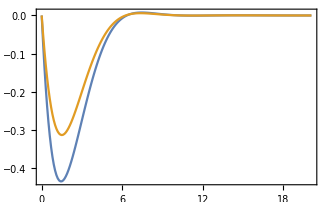

```mathematica
Module[{list1, list2},
list1 =Chop@solCs[[2]] ;
list2=Chop@solQs[[2]];
ListLinePlot[{list1,list2},
PlotRange->{All(*{0,2}*),All}]
]
```

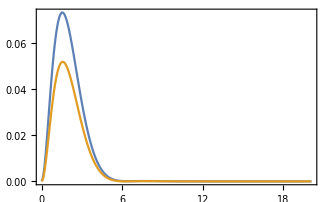

```mathematica
Module[{list1, list2},
list1 =Chop@solCs[[3]] ;
list2=Chop@solQs[[3]];
ListLinePlot[{list1,list2},
PlotRange->{All(*{0,2}*),All}]
]
```

The probability of the excited state as a function of time:

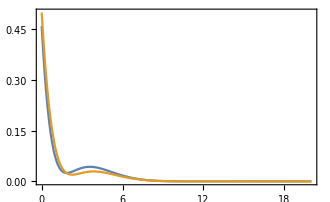

The probability of the ground state as a function of time:

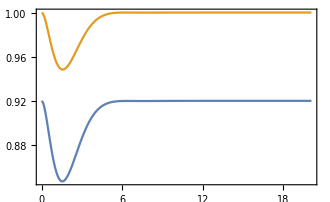

```mathematica
Module[{list1, list2},
list1 =Chop@solCs[[4]] ;
list2=Chop@solQs[[4]];
ListLinePlot[{list1,list2},
PlotRange->{All(*{0,2}*),All}]
]
```

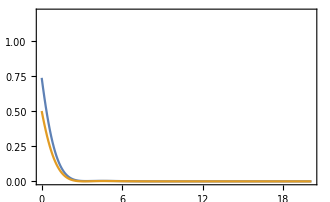

```mathematica
Module[{list1, list2},
list1 =Chop@solCs[[5]] ;
list2=Chop@solQs[[5]];
ListLinePlot[{list1,list2},
PlotRange->{All,{0,1.2}}]
]
```

## ??. Spin-measurement: 4LS interacting with left and right polarizations

## I. Hilbert space and operators definition

In this section I:
	1) Define the Hilbert space structure and the operators of the four-level system (4LS) and the two circular polarization fields R and L;
	2) ℋ_Tot= ℋ_(4LS)x ℋ_Rx ℋ_L

```mathematica
(*4LS dimension and basis vectors*)
dim4LS = 4;
{trionUp, trionDw, spinUp,spinDw} =Table[ Basis[dim4LS,i], {i,1,4}] ;

(*Defines a single Fock space*)
dimFock =4; (*80; This works for 10 photons*)
numberState[n_]:=Basis[dimFock,n+1];
LoadBosonicOperators[dimFock];
ℐFock=Eye[dimFock];

(*Right and Left bosonic operators*)
𝕒R=kron[Eye[4],a,ℐFock];
𝕒L=kron[Eye[4],ℐFock,a];
𝕒H=(𝕒R + 𝕒L)/(√2);
𝕒V=ⅇ^(ⅈ π/2)((𝕒R - 𝕒L)/(√2));
𝕒A=ⅇ^(-ⅈ π/4)((𝕒R - ⅈ 𝕒L)/(√2));
𝕒D=ⅇ^(ⅈ π/4)((𝕒R + ⅈ 𝕒L)/(√2));

(*Polarization dipole vectors*)
ΣR = out[spinUp,trionUp]//mf;
ΣL = out[spinDw,trionDw]//mf;
ΣH = (ΣR + ΣL)/(√2);
ΣV=ⅇ^(ⅈ π/2)((ΣR - ΣL)/(√2));
ΣA=ⅇ^(-ⅈ π/4)((ΣR - ⅈ ΣL)/(√2));
ΣD=ⅇ^(ⅈ π/4)((ΣR + ⅈ ΣL)/(√2));

σR=kron[ΣR,ℐFock,ℐFock];
σL=kron[ΣL,ℐFock,ℐFock];
σH =kron[ΣL,ℐFock,ℐFock];
σV =kron[ΣL,ℐFock,ℐFock];
σA =kron[ΣL,ℐFock,ℐFock];
σD =kron[ΣL,ℐFock,ℐFock];

(*Pauli-sh operators in the spin subspace - esc-scs-esc.*)
𝓈x = kron[out[spinUp,spinDw]+out[spinDw,spinUp],ℐFock,ℐFock];
𝓈y =kron[ -ⅈ out[spinUp,spinDw]+ⅈ out[spinDw,spinUp],ℐFock,ℐFock];
𝓈z = kron[out[spinUp,spinUp] - out[spinDw,spinDw],ℐFock,ℐFock];
𝓈m = kron[out[spinDw, spinUp],ℐFock,ℐFock];

𝓈vec = {𝓈x,𝓈y,𝓈z};

(*Pauli-sh operators in the trion subspace- esc-dss-esc.*)
𝕤x = kron[out[trionUp,trionDw]+out[trionDw,trionUp],ℐFock,ℐFock];
𝕤y = kron[-ⅈ out[trionUp,trionDw]+ⅈ out[trionDw,trionUp],ℐFock,ℐFock];
𝕤z = kron[out[trionUp,trionUp] - out[trionDw,trionDw],ℐFock,ℐFock];
𝕤m = kron[out[trionDw, trionUp],ℐFock,ℐFock];
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 1 | 0 | 0)

### 2) Physical Problem definition

Now I write the code that will evolve the joint state in time following Mølmer’s approach.
We have in to provide in total 8 parameters:
	Pulse parameter:
	1) Γ = Pulse bandwidth (Variable for us).
	System parameters:
	2) γ = vacuum decay rate (= 1 for us)
	3) ω0 = system natural frequency
	4) ωs=source natural frequency
	Phenomenological parameters:
	5)ηs = source efficiency (= 1 ideally)
	6) η = total efficiency (=1 ideally). Equivalent to a→√η a
	Source and spin phenomenological dephasings: 
	7) γ^⋆=γstar = spin dephasing (= 0 ideally)
	8) κ^⋆=κstar = light dephasing (= 0 ideally)

Na verdade eu to pouco me lixando pro estado do campo, o que eu quero é o estado do 4LS e quantidades associadas a ele.

Dito isto, eu posso simplificar o meu codigo fazendo um traço parcial sobre o campo e guardando so a matrix de densidade do 4LS.

```mathematica
Clear[stateEvolution4LS];

stateEvolution4LS[ρ0_, tf_,Γ_,κst_,γ_:1,ω0_:0,ωc_:0,ηs_:1,η_:1,γstar_:0,κstar_:0,Δt_:0.1] :=

 Module[{ρt,aux,ρtvec,TimeDependentRatesTable, TimeDependentHamiltonianTable,len,ℒt,ρUnvect ,ρ4LS},

aux = κst/.κs->Γ;

(*Vectorize the initial state*)
ρtvec = Vec[ρ0];

(*Start a list keeping the times and the state of the 4LS at that time*)
ρlist = {{0,PTr[ρ0,{2,3}, {dim4LS,dimFock,dimFock}]}};

(*Make a list with all the time dependent rates, the first argument is the spontaneous emission γ, the second is the rate itself, for the case of an exponential decay it reduces to Γ, BUT IT CAN BE ANY FUNCTION OF t (constant for a decreasing pulse*)

TimeDependentRatesTable= Table[{γ, aux}, {t, 0, tf, Δt}];

(*Compute the length of this list*)
len = Length[TimeDependentRatesTable];

(*Make a list of the time dependent Hamiltonians, for each time the Hamiltonian will have a definite value*)
TimeDependentHamiltonianTable =Table[ ω0(σR†.σR+σL†.σL) + ωc η( 𝕒R†.𝕒R+𝕒L†.𝕒L)-ⅈ/2(γ TimeDependentRatesTable[[k,2]] )^(1/2)√η(σR†.𝕒R - σR.𝕒R†+σL†.𝕒L - σL.𝕒L†), {k, 1, len}];

(*The following Do evolves the joint state in time*)

Do[
(*Compute the vectorized Liouvillian with time indexed by k*)
ℒt = UnitaryToVec[TimeDependentHamiltonianTable⟦k⟧](*Unitary evolution*)+LindbladToVec[√γ σR + √(ηs Γ)𝕒R](*Decay in R*)+LindbladToVec[√γ σL+ √(ηs Γ)𝕒L](*Decay in L*)+LindbladToVec[√(1-ηs Γ)𝕒R]+LindbladToVec[√(1-ηs Γ)𝕒L]+LindbladToVec[√γstar(σR†.σR+σL†.σL)](*Pure dephasing of the 4LS*)+LindbladToVec[√(κstar η)(𝕒R†.𝕒R+𝕒L†.𝕒L)];(*Pure dephasing of light*)

(*Evolve the vectorized state by Δt, updating it.*)
ρtvec = MatrixExp[ℒt Δt,ρtvec];

(*Unvectorize obtaining the full density matrix*)
ρt=Unvec@ρtvec;

(*Do a partial trace over the field fo obtain the 4LS density matrix*)
ρ4LS = PTr[ρt,{2,3}, {dim4LS,dimFock,dimFock}];

(*Append to the list the time and density matrix for 4LS at this point of time*)
AppendTo[ρlist, {k Δt, ρ4LS }],

(*Sweep for all times*)
{k, 1, len}];

(*Return the ρ4LS list containing the times and operators*)
ρlist]

stateEvolution::usage = "Inputs:
  ρ0 = joint field and system initial state density matrix
  Δt= time step, 
  tf= the final time the physical ORDERED parameters 
  {ω0, ωcav, γ}= atom frequency, cavity frequency and decay rate";
```

#### Initial state of the 4LS - Nickel!

```mathematica
ψ04LS = Normalize[spinDw + spinUp]//N//mf;
ρ04LS = out[ψ04LS,ψ04LS]//mf;
```

(0
0
0.707107
0.707107)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0.5 | 0.5
0 | 0 | 0.5 | 0.5)

#### Light with quantum statistics

```mathematica
ψvacuum =kron[numberState[0],numberState[0]];(*vacuum component*)

ψR1photon =kron[numberState[0],a†.numberState[0]];(*one R-photon*)
ψL1photon =kron[a†.numberState[0],numberState[0]];(*one L-photon*)

ψH1photon =(ψR1photon+ψL1photon)/(√2);(*one H-photon*)

ψSuperpositionOfNumberStates[nbar_]:= (1-nbar)ψvacuum + nbar ψH1photon (*Superposition of vacuum and 1 H-photon with the knob "n"*)
```

```mathematica
ψSuperpositionOfNumberStates[1];
```

```mathematica
Clear[ρFSuperposition]
```

```mathematica
Do[ρFSuperposition[nbar] = out[ψSuperpositionOfNumberStates[nbar],ψSuperpositionOfNumberStates[nbar]], {nbar,10^-2,1.,0.01}]
```

```mathematica
Clear[ρTotQs];
Do[ρTotQs[nbar] = kron[ρ04LS,ρFSuperposition[nbar]], {nbar,10^-2,1.,0.01}]
```

```mathematica
Tr@ρTotQs
```

1.

```mathematica
Clear[ρtotalQSList]
PrettyTiming[
Do[ρtotalQSList[nbar]=stateEvolution4LS[ρTotQs[nbar] , 15,1,κs], {nbar,10^-2,1.,0.01}]];
```

0h : 2m : 5s

```mathematica
ρtotalQSList[0.01]
```

{{0,SparseArray[…]},{0.1,{1}},{0.2,1},146,{14.9,{1}},{15.,{1}},{15.1,{1}}}
 |  |  |  |

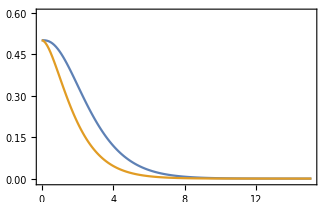

```mathematica
Module[{aux},
aux =1.;
table1=Table[{ρtotalQSList[aux][[k,1]],Chop@Tr[Πupdw.ρtotalQSList[aux][[k,2]]]},{k,1,Length@ρtotalQSList[aux]}];
table2=Table[{ρtotalQSList[aux][[k,1]],Chop@Tr[σupdw.ρtotalQSList[aux][[k,2]]]},{k,1,Length@ρtotalQSList[aux]}];

ListLinePlot[{table1,table2},PlotRange->{All,{-0.01,0.6}}]
]
```

#### Light with classical statistics

```mathematica
(*Defining the initial state of the field*)
Clear[ψR1coherent,ψL1coherent,ψH1photonCoh]
(*The coherent state in each polarization total horizotal polarization divided by the squareroot of 2,i.e., αR=αL=αH/√2*)
ψR1coherent[αH_]:=CoherentState[αH/(√2)];
ψL1coherent[αH_]:=CoherentState[αH/(√2)];
```

```mathematica
ψH1photonCoh [αH_]:= kron[ψL1coherent[αH],ψR1coherent[αH]]//N;
(*density matrix for αH = 1*)
```

```mathematica
ρFCoherent = out[ψH1photonCoh[10],ψH1photonCoh[10]];
```

```mathematica
(*Sanity chack: is the photonic density matrices normalized?*)
Tr@ρFCoherent//N
```

0.999887

0.9965

```mathematica
ρTotCs = kron[ρ04LS,ρFCoherent]
```

SparseArray[…]

```mathematica
PrettyTiming[ρtotalCSList=stateEvolution4LS[ρTotCs, 15,1,κs]];
```

0h : 0m : 2s

```mathematica
Πupdw = out[trionUp,trionDw]+out[spinUp,spinDw]//mf;
σupdw = out[spinUp,spinDw]//mf;
```

(0 | 1 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 0)

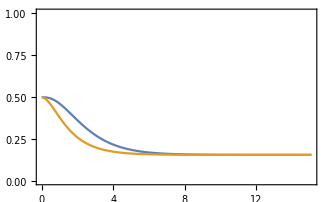

```mathematica
table3=Table[{ρtotalCSList[[k,1]],Abs@Chop@Tr[Πupdw.ρtotalCSList[[k,2]]]},{k,1,Length@ρtotalCSList}];
table4=Table[{ρtotalCSList[[k,1]],Abs@Chop@Tr[σupdw.ρtotalCSList[[k,2]]]},{k,1,Length@ρtotalCSList}];

ListLinePlot[{table3,table4},PlotRange->{All,{0,1}}]
```

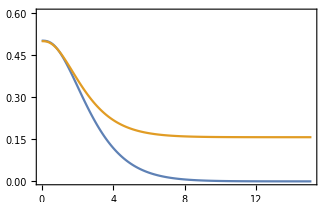

```mathematica
ListLinePlot[{table1(*,table2*),table3(*,table4*)},PlotRange->{All,{0,0.6}}]
```

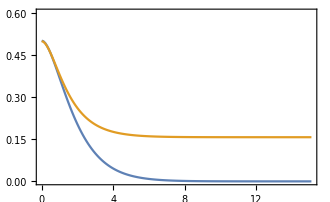

```mathematica
ListLinePlot[{table2,table4},PlotRange->{All,{0,0.6}}]
```

```mathematica
ρtotalCSList[[Length@ρtotalCSList,2]]
```

{{0.0000129678+0. ⅈ,6.09129×10^-6+0. ⅈ,-0.00248192+0. ⅈ,-0.000977648+0. ⅈ},{6.09129×10^-6+0. ⅈ,0.0000129678+0. ⅈ,-0.000977648+0. ⅈ,-0.00248192+0. ⅈ},{-0.00248192+0. ⅈ,-0.000977648+0. ⅈ,0.498237+0. ⅈ,0.156912+0. ⅈ},{-0.000977648+0. ⅈ,-0.00248192+0. ⅈ,0.156912+0. ⅈ,0.498237+0. ⅈ}}

```mathematica
ρtotalCSList[[-1,2]]//mf;
```

(0.0000129678 | 6.09129×10^-6 | -0.00248192 | -0.000977648
6.09129×10^-6 | 0.0000129678 | -0.000977648 | -0.00248192
-0.00248192 | -0.000977648 | 0.498237 | 0.156912
-0.000977648 | -0.00248192 | 0.156912 | 0.498237)

#### testing an idea

```mathematica
α=√(n Γ)Exp[-Γ/2 t]
```

ⅇ^(-(t Γ)/2) √(n Γ)

```mathematica
Assuming[Γ > 0,Integrate[α^2,{t,0,∞}]]
```

n

```mathematica
√(n Γ)Exp[-Γ/2 t]
```

```mathematica
Htest =(ΣH†-ΣH)//mf;
```

(0 | 0 | 1/(√2) | 0
0 | 0 | 0 | 1/(√2)
-1/(√2) | 0 | 0 | 0
0 | -1/(√2) | 0 | 0)

```mathematica
ℒtest = Liouvillian[Htest,{√γ ΣR,√γ ΣL}]//cf//mf;
```

(-γ | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -γ | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0
ⅈ/(√2) | 0 | -γ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0
0 | ⅈ/(√2) | 0 | -γ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -γ | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -γ | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0 | 0
0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | -γ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2) | 0
0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | -γ/2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -ⅈ/(√2)
ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ/2 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0 | 0
0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ/2 | 0 | -ⅈ/(√2) | 0 | 0 | 0 | 0
γ | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ/2 | 0 | -ⅈ/(√2) | 0
0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -γ/2 | 0 | -ⅈ/(√2)
0 | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | γ | 0 | ⅈ/(√2) | 0 | 0 | 0 | 0 | 0 | ⅈ/(√2) | 0 | 0)

```mathematica
ρss = AnalyticalSteadyState[ℒtest]//mf;
```

(-2/(-4+γ^2) | 0 | -(ⅈ √2 γ)/(-4+γ^2) | 0
0 | 0 | 0 | 0
-(ⅈ √2 γ)/(-4+γ^2) | 0 | (-2+γ^2)/(-4+γ^2) | 0
0 | 0 | 0 | 0)

```mathematica
Tr@ρss//cf
```

1

```mathematica
Πx = out[spinUp,spinDw]+out[spinDw,spinUp]//mf;
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0)

```mathematica
Tr[Πx.ρss]
```

0

```mathematica
ContourPlot[((ⅇ^(t Γ) γ^2-2 n Γ)/(ⅇ^(t Γ) γ^2-4 n Γ))/.γ->1/.Γ->ΓΓ/.t,]
```

### Implementing source dephasing

Now

```mathematica
Length@Table[κstar,{κstar,10^-3,10^3,100}]
```

10

```mathematica
spincoherenceasfunctionofsourcedephasinglist = {};
Do[
PrettyTiming[ρtotalCSList=stateEvolution4LS[ρTotCs, 30,1,κs,1,0,0,1,1,0,κstar,0.3]];

AppendTo[spincoherenceasfunctionofsourcedephasinglist,{κstar,Tr[Πupdw.ρtotalCSList[[-1,2]]]}],

{κstar,10^-3,10^3,100}]
```

0h : 0m : 1s

0h : 0m : 1s

0h : 0m : 2s

0h : 0m : 1s

0h : 0m : 2s

Divide::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Divide::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Divide::infy will be suppressed during this calculation.

0h : 0m : 2s

0h : 0m : 3s

0h : 0m : 3s

0h : 0m : 3s

«1 more identical outputs»

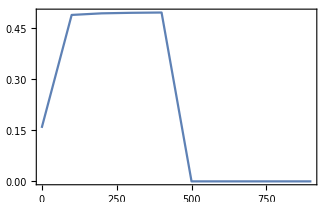

```mathematica
ListLinePlot[spincoherenceasfunctionofsourcedephasinglist]
```

```mathematica
tableQS=Table[{ρspQSList[[k,1]],Abs@Chop@Tr[σUpDw.ρspQSList[[k,2]]]},{k,1,Length@ρspQSList}];
```

```mathematica
tableCSσx=Table[{ρspCSList[[k,1]],(Abs@Chop@Tr[σxspin.ρspCSList[[k,2]]])},{k,1,Length@ρspCSList}];
tableQSσx=Table[{ρspQSList[[k,1]],(Abs@Chop@Tr[σxspin.ρspQSList[[k,2]]])},{k,1,Length@ρspQSList}];
```

```mathematica
tableCSσUpDw=Table[{ρspCSList[[k,1]],(Abs@Chop@Tr[σUpDw.ρspCSList[[k,2]]])},{k,1,Length@ρspCSList}];
tableQSσUpDw=Table[{ρspQSList[[k,1]],(Abs@Chop@Tr[σUpDw.ρspQSList[[k,2]]])},{k,1,Length@ρspQSList}];
```

```mathematica
tableCSexc=Table[{ρspCSList[[k,1]],(Chop@Tr[excitationoperator.ρspCSList[[k,2]]])},{k,1,Length@ρspCSList}];
tableQSexc=Table[{ρspQSList[[k,1]],(Chop@Tr[excitationoperator.ρspQSList[[k,2]]])},{k,1,Length@ρspQSList}];
```

Part::partd: Part specification alphabetlabel⟦1⟧ is longer than depth of object.

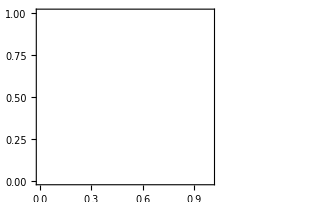

```mathematica
spinCoherence=ListLinePlot[{tableQSσx,tableCSσx},
PlotStyle->{Red,Blue},
Epilog->Inset[Style[alphabetlabel[[1]],20],{5,0.9}],
(*PlotLegends->legend[{"n=1_H","α=1_H"},{0.8,0.78}],*)
PlotRange->All]
```

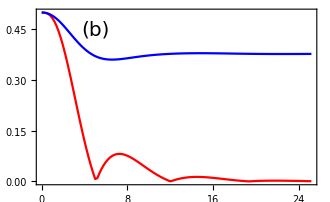

```mathematica
totalCoherence=ListLinePlot[{tableQSσUpDw,tableCSσUpDw},
PlotStyle->{Red,Blue},
Epilog->Inset[Style[alphabetlabel[[2]],20],{5,0.45}],
(*PlotLegends->legend[{"n=1_H","α=1_H"},{0.8,0.78}],*)
PlotRange->All]
```

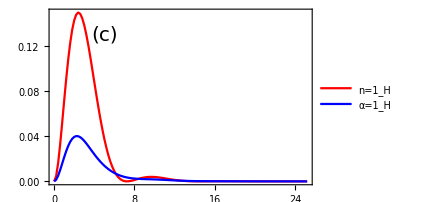

```mathematica
excitationplot=ListLinePlot[{tableQSexc,tableCSexc},
PlotStyle->{Red,Blue},
Epilog->Inset[Style[alphabetlabel[[3]],20],{5,0.13}],
PlotLegends->legend[{"n=1_H","α=1_H"},{0.8,0.77}],
PlotRange->All]
```

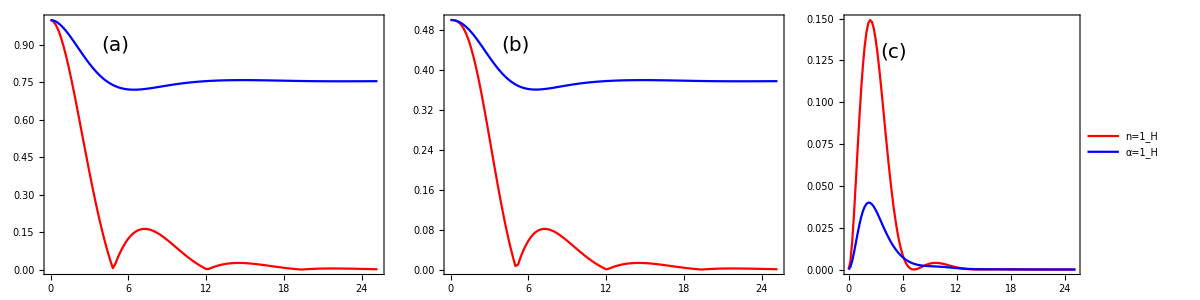

```mathematica
Grid[{{spinCoherence,totalCoherence,excitationplot}}]
```

## Pulse temporal shapes: decreasing exponential and gaussian profile

Pulse shapes temporal profiles:
f  = decreasing exponential
g = gaussian pulse

### Computing the qBhat for the quantum state

#### Decreasing exponential pulse

```mathematica
Clear[Γ];
f=√(n κs) Exp[-κs/2 t]
Assuming[κs>0,Integrate[(f//cf)^2,{t,0,∞}]]
```

ⅇ^(-(t κs)/2) √(n κs)

n

```mathematica
integrand = Exp[(γ/2+ⅈ ω0)u] √(n κs) Exp[-κs/2 u]//cf;
βtildef = Integrate[integrand,{u,0,t}]
```

(2 (-1+ⅇ^(1/2 t (γ-κs+2 ⅈ ω0))) √(n κs))/(γ-κs+2 ⅈ ω0)

```mathematica
integrand2 = f βtildef Exp[-ⅈ ω0 t]/.ω0->0//cf
```

(2 ⅇ^(-(t κs)/2) (-1+ⅇ^(1/2 t (γ-κs))) n κs)/(γ-κs)

```mathematica
Integrate[integrand2,{t,0,∞}]
```

ConditionalExpression[-(4 n)/(γ-2 κs), Re[γ-2 κs]<0&&Re[κs]>0]

```mathematica
1+γ(-(4 n)/(γ-2 κs))//cf
```

1-(4 n γ)/(γ-2 κs)

#### Gaussian pulse

```mathematica
g=((16 κs^2 Log[4])/π)^(1/4)Exp[-4 Log[2] κs^2 t^2 ]//cf
Assuming[κs>0,Integrate[(g//cf)^2,{t,0,∞}]]
```

2^(1-4 t^2 κs^2) √κs (Log[4]/π)^(1/4)

1

```mathematica
integrand = Exp[(γ/2+ⅈ ω0)u]((16 κs^2 Log[4])/π)^(1/4)Exp[-4 Log[2] κs^2 u^2 ]//cf;
βtildeg = Integrate[integrand,{u,0,t}]
```

(ⅇ^((γ+2 ⅈ ω0)^2/(64 κs^2 Log[2])) (Erf[(γ+2 ⅈ ω0)/(8 κs √Log[2])]-Erf[(γ+2 ⅈ ω0-16 t κs^2 Log[2])/(8 κs √Log[2])]) (π Log[4])^(1/4))/(2 √κs √Log[2])

```mathematica
integrand2 = g βtildeg Exp[-ⅈ ω0 t]/.ω0->0//cf
```

2^(1/2-4 t^2 κs^2) ⅇ^(γ^2/(64 κs^2 Log[2])) (Erf[γ/(8 κs √Log[2])]-Erf[(γ-16 t κs^2 Log[2])/(8 κs √Log[2])])

```mathematica
Integrate[integrand2,{t,0,∞}]
```

∫_0^∞ 2^(1/2-4 t^2 κs^2) ⅇ^(γ^2/(64 κs^2 Log[2])) (Erf[γ/(8 κs √Log[2])]-Erf[(γ-16 t κs^2 Log[2])/(8 κs √Log[2])])ⅆt

```mathematica
1+γ%
```

1+γ ∫_0^∞ 2^(1/2-4 t^2 κs^2) ⅇ^(γ^2/(64 κs^2 Log[2])) (Erf[γ/(8 κs √Log[2])]-Erf[(γ-16 t κs^2 Log[2])/(8 κs √Log[2])])ⅆt

```mathematica
Table[1-NIntegrate[(integrand2/.κs->Γ/.γ->1),{t,0,∞}],{Γ,10^-2,1,10^-1}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{1.,-11.1745,-2.13526,-0.736468,-0.194161,0.0914693,0.267288,0.386269,0.472087,0.536891}

The virtual cavity decay rates for each temporal profile of the pulse, as a function of the pulse badwidth Γ, is given by

```mathematica
hf = f^2/(1-Integrate[(f^2/.t->u),{u,0,t}])//cf
```

κs

```mathematica
hg = g^2/(1-Integrate[(g^2/.t->u),{u,0,t}])//cf
```

(4^(1-4 t^2 κs^2) κs √(Log[4]/π))/Erfc[2 t κs √Log[4]]

```mathematica
numberState[0]
```

SparseArray::posd: The left-hand side of 0→1 in {0→1} is not a position or a pattern that will match the position of an element in an array with dimensions {5}.

SparseArray[{0→1},5]

## Trash bin

```mathematica
Clear[stateEvolution4LS];

stateEvolution4LS[ρ0_, tf_,Γ_,virtualCavitydecayrate_,γ_:1,ω0_:0,ωc_:0,ηs_:1,η_:1,γstar_:0,κstar_:0,Δt_:0.2] :=

 Module[{ρt,aux,ρtvec,TimeDependentRatesTable, TimeDependentHamiltonianTable,len,ℒt,ρUnvect ,ρsp},
(*Vectorize the initial state*)
aux = virtualCavitydecayrate/.κs->Γ;
ρt = Vec[ρ0];

(*Start a list keeping the times and the joint state at that time*)
ρlist = {{0,ρ0}};

(*Start a list keeping the times and the 4LS state at that time*)
(*ρ4LSlist={{0,PTr[ρ0,{2,3},systemsDimensions]}};*)
Print[4];
(*Make a list with all the time dependent rates, the first argument is the spontaneous emission γ, the second is the rate itself, for the case of an exponential decay it reduces to Γ, BUT IT CAN BE ANY FUNCTION OF t (constant for a decreasing pulse*)
Print[5];
TimeDependentRatesTable= Table[{γ, aux}, {t, 0, tf, Δt}];

(*Compute the length of this list*)
len = Length[TimeDependentHamiltonianTable];

Print[6];
(*Make a list of the time dependent Hamiltonians, for each time the Hamiltonian will have a definite value*)
TimeDependentHamiltonianTable =Table[ ω0(σR†.σR+σL†.σL) + ωc η( 𝕒R†.𝕒R+𝕒L†.𝕒L)-ⅈ/2 √(γ TimeDependentRatesTable[[k,2]])√η(σR†.𝕒R - σR.𝕒R†+σL†.𝕒L - σL.𝕒L†), {k, 0, len}];

(*The following Do evolves the joint state in time*)

Do[
(*Compute the vectorized Liouvillian with time indexed by k*)
ℒt = 
UnitaryToVec[TimeDependentHamiltonianTable⟦k⟧](*Unitary evolution*)
+LindbladToVec[√γ σR](*Decay in R*)
+LindbladToVec[√γ σL](*Decay in L*)
+LindbladToVec[√γstar(σR†.σR+σL†.σL)](*Pure dephasing of the 4LS*)
+LindbladToVec[√(κstar η)(𝕒R†.𝕒R+𝕒L†.𝕒L)];(*Pure dephasing of light*)

(*Evolve the vectorized state by Δt, updating it.*)
ρtvec = MatrixExp[ℒt Δt,ρt];

(*Unvectorize obtaining the full densityt matrix*)
ρt=Unvec@ρtvec;
(*Do a partial trace over the field fo obtain the 4LS density matrix*)
(*ρsp =PTr[ρUnvect ,{2,3}, systemsDimensions];*)

(*Print[{k Δt,ρsp//mf};];*)
(*Append to the list the time and density matrix for the joint an the 4LS at this point of time, notice the unvectorization of the ρt*)
AppendTo[ρlist, {k Δt, ρt }],
(*AppendTo[ρ4LSlist, {k Δt, ρsp}],*)
(*Sweep for all times*)
{k, 1, len}];
(*Return the ρ list containing the times and operators*)
ρlist(*{ρlist,ρ4LSlist}*)]

stateEvolution::usage = "Inputs:
  ρ0 = joint field and system initial state density matrix
  Δt= time step, 
  tf= the final time the physical ORDERED parameters 
  {ω0, ωcav, γ}= atom frequency, cavity frequency and decay rate";
```